```mathematica
L=40;
tab=Table[{x,1/((L/π)Sin[x π/L])^(1/4)},{x,1,L/2}];
```

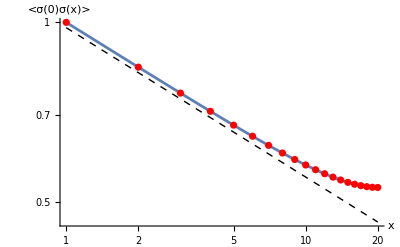

```mathematica
Show[LogLogPlot[0.98/(y)^(1/4),{y,1,20},PlotStyle->{Black,Dashed,Thin}],LogLogPlot[1/((L/π)Sin[x π/L])^(1/4),{x,1,20}],ListLogLogPlot[tab, PlotStyle->Red],AxesLabel->{"x","<σ(0)σ(x)>"}]
```

```mathematica
L=40;
tab=Table[{(L/π)Sin[x π/L],1/((L/π)Sin[x π/L])^(1/4)},{x,1,L/2}];
```

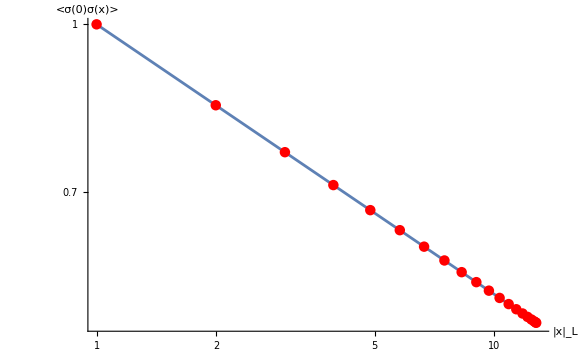

```mathematica
Show[LogLogPlot[1/y^(1/4),{y,1,13}],ListLogLogPlot[tab, PlotStyle->Red],AxesLabel->{"|x|_L","<σ(0)σ(x)>"}]
```

```mathematica
f[x2_,x3_,L_]:=0.5N[hd[x2,L]^-1 hd[x3,L]^-1 hd[Abs[x2-x3],L]^(3/4)]
hd[x_,L_]:=L/π Sin[π/L Abs[x]];
```

```mathematica
Plot3D[f[x2,x3,40],{x2,0,40},{x3,0,40},PlotPoints->100,PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>",AxesLabel->{"x_2","x_3"},PlotRange->{0,10^-0.5}]
```

-Graphics3D-

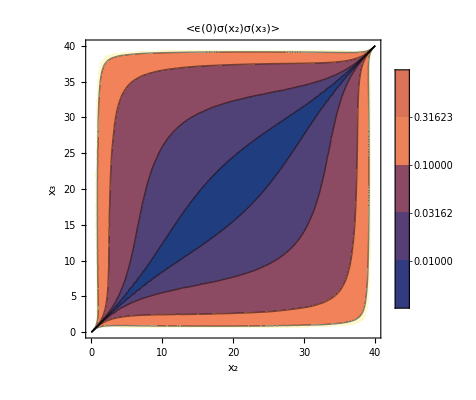

```mathematica
plot=ContourPlot[f[x2,x3,40],{x2,0,40},{x3,0,40},Contours->{10^-2,10^-1.5,10^-1,10^-0.5},PlotLegends->{10^-2,10^-1.5,10^-1,10^-0.5,1},PlotLabel->"<ϵ(0)σ(x_2)σ(x_3)>",FrameLabel->{"x_2","x_3"}]
```

```mathematica
Export["/Users/slava/Personal/----Fisica----/_Projects/Fork/2025 three_point_function_CFT/fig-eps-sig-sig-theory.pdf",Rasterize[plot,"Image"]];
```